```mathematica
x[t_, a_, b_, c_, d_]:= a + b t + c t^2 +d t^3
```

```mathematica
data = {x0 -> 0, x1 ->2, tf->1};
```

```mathematica
fullPhi = {x[0, a, b, c, d] == x0, x[tf, a, b, c, d]==x1, (D[x[t, a, b, c, d], t]/.{t->0})==0, (D[x[t, a, b, c, d], t]/.{t->tf})==0}; 
reducedPhi = {x[0, a, b, c, d] == x0, x[tf, a, b, c, d]==x1}; fullPhi//MatrixForm
reducedPhi//MatrixForm
```

(a==x0
a+b tf+c tf^2+d tf^3==x1
b==0
b+2 c tf+3 d tf^2==0)

(a==x0
a+b tf+c tf^2+d tf^3==x1)

```mathematica
sol1 = Solve[fullPhi, {a, b, c, d}]
sol2 = Solve[reducedPhi, {a, c}]
```

{{a→x0,b→0,c→-(3 (x0-x1))/tf^2,d→(2 (x0-x1))/tf^3}}

{{a→x0,c→-(b tf+d tf^3+x0-x1)/tf^2}}

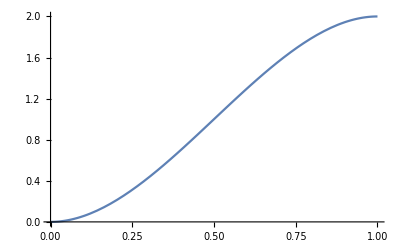

```mathematica
Plot[x[t, a, b, c, d]/.sol1[[1]]/.data, {t, 0,1}, PlotRange->Automatic]
```